```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
S[basissize_] := Transpose[Normalize /@ Eigenvectors[x[basissize]]];
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
```

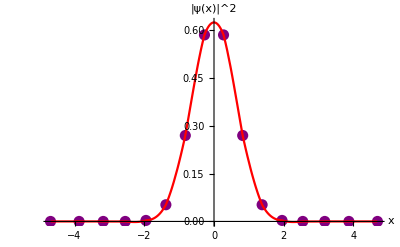

```mathematica
n = 0; bs = 16; g=.275;
e0wfvqe = {0.9941625159144055,0,-0.10789296525139842,0,0,0,0,0,0,0,0,0,0,0,0,0};
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
funvqe = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2}]];
norm2vqe= NIntegrate[funvqe[x],{x,-4.68,4.68}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2/norm2vqe}],PlotRange->All,PlotStyle->{Purple,AbsolutePointSize[8]}];
p3 = Plot[funvqe[x]/norm2vqe,{x,-4.68,4.68},PlotStyle->Hue[1]];
plot = Show[p2,p3,PlotRange->All,AxesLabel->{"x","|ψ(x)|^2"}]
(* ShowLegend seems to be deprecated... *)
ShowLegend[plot,{{{Graphics[{Purple, Disk[{0,0},.05]}],"Discrete VQE"},{Graphics[{Thickness[.1],Red,Line[{{0,0},{2,0}}]}],"VQE Interpolation"}},LegendPosition->{0.1,0.1},LegendSize->{0.6,0.4},LegendShadow->False}];
```